```mathematica
(*TBH FORMATION*)
```

```mathematica
R=5*10^6;(*in m*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
M=1.1*2*10^30;(*in kg*)
```

```mathematica
vesc=((2*G*M)/R)^0.5;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
ρ=6*10^10;(*in kg/m^3*)
```

```mathematica
n=ρ/(12*1.78*10^-27);(*in m^-3*)
```

```mathematica
Nn=4/3*π*R^3*n;
```

```mathematica
ρx=10^6*0.4(*in GeV/m^3*);
```

```mathematica
mn=12;(*in GeV*)
mp=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
mup[mx_?NumericQ]:=(mp*mx)/(mp+mx);
```

```mathematica
sigmasat=(π*R^2)/Nn;(*DM-carbon saturation cross section*)
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
fMB[u_?NumericQ]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
c=3*10^8;
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+4*mr[mx]^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
Λ=(0.91*mn^(1/3)+0.3)*5;(*in GeV^-1*)
ei=3/(2*mn*Λ^2);(*in GeV*)
er[mx_]:=(mx^2*mn)/(mn+mx)^2*(10^-2)^2;(*in GeV*)
helm[mx_]:=Exp[(-er[mx])/ei];
```

```mathematica
auni[mx_?NumericQ,sigma_?NumericQ]:=Min[(mr[mx]/mup[mx])^2*12^2*helm[mx]*sigma,sigmasat]*ρx/mx*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*(1-1/βplus[mx]*u^2/(u^2+vesc^2)),{u,0,vesc/(1/βplus[mx]-1)^0.5}];
agen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=Min[(mr[mx]/mup[mx])^2*12^2*helm[mx]*sigma,sigmasat]*ρx/mx*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*g1[u,mx,mphi],{u,0,vesc/(1/βplus[mx]-1)^0.5}];
```

```mathematica
tage=9*10^9*3.15*10^7;

rth[mx_?NumericQ,T_?NumericQ]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
totcapuni[mx_?NumericQ,sigma_?NumericQ]:=  auni[mx,sigma]*tage;
totcapgen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=  agen[mx,sigma,mphi]*tage;
```

```mathematica
Nself[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*ρ*1/(mx*1.78*10^-27);

Mpl=1.2211*10^19;
NchBoson[mx_?NumericQ]:=2/π*Mpl^2/mx^2;
NchFermion[mx_?NumericQ]:=Mpl^3/mx^3;
```

```mathematica
GN=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
cwd=0.03;
λ=0.25;
```

```mathematica
mcrit=1/GN*(cwd^3/(74*π*4*π*λ*ρ*5.62*10^26*(1.98*10^-16)^3))^0.25;(*critical mass for BH evaporation in GeV*)
```

```mathematica
mcrit
```

5.13995×10^38

```mathematica
rth[10^6,10^7](*in m*)
```

117.79

```mathematica
Nself[10^6,10^7]
```

2.3075×10^38

```mathematica
FindRoot[10^x*Max[Nself[10^x,10^7],NchBoson[10^x]]==mcrit,{x,0}]//Quiet
```

{x→9.76812}

```mathematica
FindRoot[10^x*Max[Nself[10^x,10^7],NchFermion[10^x]]==mcrit,{x,0}]//Quiet
```

{x→9.76812}

```mathematica
10^9.76812
```

5.863×10^9

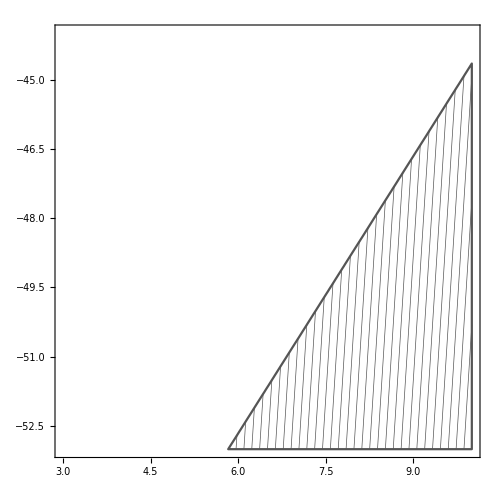

```mathematica
ttherm[mx_?NumericQ,sigma_?NumericQ,T_]:=20*3.15*10^7*(10^-44/sigma)*(mx/10^6)^2*(10^7/T)^(5/2);
RegionPlot[{ttherm[10^x,10^y,10^7]≥  tage},{x,3,10},{y,-44,-53},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],BoundaryStyle->Darker[Gray],PlotStyle->Directive[White,Opacity[0.4]],MeshFunctions->{20*#1-#2&},Mesh->30,MeshStyle->Directive[Darker[Gray],Thickness[0.001]],PlotRangePadding->None,ImageSize->500]
```

```mathematica
myticks={{{{-42,"10^-38",{0.020,0}},{-44,"10^-40",{0.020,0}},{Log10[9*10^-45],"",{0.010,0}},{Log10[8*10^-45],"",{0.010,0}},{Log10[7*10^-45],"",{0.010,0}},{Log10[6*10^-45],"",{0.010,0}},{Log10[5*10^-45],"",{0.010,0}},{Log10[4*10^-45],"",{0.010,0}},{Log10[3*10^-45],"",{0.010,0}},{Log10[2*10^-45],"",{0.010,0}},{-45,"10^-41",{0.020,0}},{Log10[9*10^-46],"",{0.010,0}},{Log10[8*10^-46],"",{0.010,0}},{Log10[7*10^-46],"",{0.010,0}},{Log10[6*10^-46],"",{0.010,0}},{Log10[5*10^-46],"",{0.010,0}},{Log10[4*10^-46],"",{0.010,0}},{Log10[3*10^-46],"",{0.010,0}},{Log10[2*10^-46],"",{0.010,0}},{-46,"10^-42",{0.020,0}},{Log10[9*10^-47],"",{0.010,0}},{Log10[8*10^-47],"",{0.010,0}},{Log10[7*10^-47],"",{0.010,0}},{Log10[6*10^-47],"",{0.010,0}},{Log10[5*10^-47],"",{0.010,0}},{Log10[4*10^-47],"",{0.010,0}},{Log10[3*10^-47],"",{0.010,0}},{Log10[2*10^-47],"",{0.010,0}},{-47,"10^-43",{0.020,0}},{Log10[9*10^-48],"",{0.010,0}},{Log10[8*10^-48],"",{0.010,0}},{Log10[7*10^-48],"",{0.010,0}},{Log10[6*10^-48],"",{0.010,0}},{Log10[5*10^-48],"",{0.010,0}},{Log10[4*10^-48],"",{0.010,0}},{Log10[3*10^-48],"",{0.010,0}},{Log10[2*10^-48],"",{0.010,0}},{-48,"10^-44",{0.020,0}},{Log10[9*10^-49],"",{0.010,0}},{Log10[8*10^-49],"",{0.010,0}},{Log10[7*10^-49],"",{0.010,0}},{Log10[6*10^-49],"",{0.010,0}},{Log10[5*10^-49],"",{0.010,0}},{Log10[4*10^-49],"",{0.010,0}},{Log10[3*10^-49],"",{0.010,0}},{Log10[2*10^-49],"",{0.010,0}},{-49,"10^-45",{0.020,0}},{Log10[9*10^-50],"",{0.010,0}},{Log10[8*10^-50],"",{0.010,0}},{Log10[7*10^-50],"",{0.010,0}},{Log10[6*10^-50],"",{0.010,0}},{Log10[5*10^-50],"",{0.010,0}},{Log10[4*10^-50],"",{0.010,0}},{Log10[3*10^-50],"",{0.010,0}},{Log10[2*10^-50],"",{0.010,0}},{-50,"10^-46",{0.020,0}},{Log10[9*10^-51],"",{0.010,0}},{Log10[8*10^-51],"",{0.010,0}},{Log10[7*10^-51],"",{0.010,0}},{Log10[6*10^-51],"",{0.010,0}},{Log10[5*10^-51],"",{0.010,0}},{Log10[4*10^-51],"",{0.010,0}},{Log10[3*10^-51],"",{0.010,0}},{Log10[2*10^-51],"",{0.010,0}},{-51,"10^-47",{0.020,0}},{Log10[9*10^-52],"",{0.010,0}},{Log10[8*10^-52],"",{0.010,0}},{Log10[7*10^-52],"",{0.010,0}},{Log10[6*10^-52],"",{0.010,0}},{Log10[5*10^-52],"",{0.010,0}},{Log10[4*10^-52],"",{0.010,0}},{Log10[3*10^-52],"",{0.010,0}},{Log10[2*10^-52],"",{0.010,0}},{-52,"10^-48",{0.020,0}},{Log10[9*10^-53],"",{0.010,0}},{Log10[8*10^-53],"",{0.010,0}},{Log10[7*10^-53],"",{0.010,0}},{Log10[6*10^-53],"",{0.010,0}},{Log10[5*10^-53],"",{0.010,0}},{Log10[4*10^-53],"",{0.010,0}},{Log10[3*10^-53],"",{0.010,0}},{Log10[2*10^-53],"",{0.010,0}},{-53,"10^-49",{0.020,0}}},None},{{{0,"1",{0.020,0}},{Log10[2],"",{0.010,0}},{Log10[3],"",{0.010,0}},{Log10[4],"",{0.010,0}},{Log10[5],"",{0.010,0}},{Log10[6],"",{0.010,0}},{Log10[7],"",{0.010,0}},{Log10[8],"",{0.010,0}},{Log10[9],"",{0.010,0}},{1,"10",{0.020,0}},{Log10[20],"",{0.010,0}},{Log10[30],"",{0.010,0}},{Log10[40],"",{0.010,0}},{Log10[50],"",{0.010,0}},{Log10[60],"",{0.010,0}},{Log10[70],"",{0.010,0}},{Log10[80],"",{0.010,0}},{Log10[90],"",{0.010,0}},{2,"10^2",{0.020,0}},{Log10[200],"",{0.010,0}},{Log10[300],"",{0.010,0}},{Log10[400],"",{0.010,0}},{Log10[500],"",{0.010,0}},{Log10[600],"",{0.010,0}},{Log10[700],"",{0.010,0}},{Log10[800],"",{0.010,0}},{Log10[900],"",{0.010,0}},{3,"10^3",{0.020,0}},{Log10[2000],"",{0.010,0}},{Log10[3000],"",{0.010,0}},{Log10[4000],"",{0.010,0}},{Log10[5000],"",{0.010,0}},{Log10[6000],"",{0.010,0}},{Log10[7000],"",{0.010,0}},{Log10[8000],"",{0.010,0}},{Log10[9000],"",{0.010,0}},{4,"10^4",{0.020,0}},{Log10[2*10^4],"",{0.010,0}},{Log10[3*10^4],"",{0.010,0}},{Log10[4*10^4],"",{0.010,0}},{Log10[5*10^4],"",{0.010,0}},{Log10[6*10^4],"",{0.010,0}},{Log10[7*10^4],"",{0.010,0}},{Log10[8*10^4],"",{0.010,0}},{Log10[9*10^4],"",{0.010,0}},{5,"10^5",{0.020,0}},{Log10[2*10^5],"",{0.010,0}},{Log10[3*10^5],"",{0.010,0}},{Log10[4*10^5],"",{0.010,0}},{Log10[5*10^5],"",{0.010,0}},{Log10[6*10^5],"",{0.010,0}},{Log10[7*10^5],"",{0.010,0}},{Log10[8*10^5],"",{0.010,0}},{Log10[9*10^5],"",{0.010,0}},{6,"10^6",{0.020,0}},{Log10[2*10^6],"",{0.010,0}},{Log10[3*10^6],"",{0.010,0}},{Log10[4*10^6],"",{0.010,0}},{Log10[5*10^6],"",{0.010,0}},{Log10[6*10^6],"",{0.010,0}},{Log10[7*10^6],"",{0.010,0}},{Log10[8*10^6],"",{0.010,0}},{Log10[9*10^6],"",{0.010,0}},{7,"10^7",{0.020,0}},{Log10[2*10^7],"",{0.010,0}},{Log10[3*10^7],"",{0.010,0}},{Log10[4*10^7],"",{0.010,0}},{Log10[5*10^7],"",{0.010,0}},{Log10[6*10^7],"",{0.010,0}},{Log10[7*10^7],"",{0.010,0}},{Log10[8*10^7],"",{0.010,0}},{Log10[9*10^7],"",{0.010,0}},{8,"10^8",{0.020,0}},{Log10[2*10^8],"",{0.010,0}},{Log10[3*10^8],"",{0.010,0}},{Log10[4*10^8],"",{0.010,0}},{Log10[5*10^8],"",{0.010,0}},{Log10[6*10^8],"",{0.010,0}},{Log10[7*10^8],"",{0.010,0}},{Log10[8*10^8],"",{0.010,0}},{Log10[9*10^8],"",{0.010,0}},{9,"10^9",{0.020,0}},{Log10[2*10^9],"",{0.010,0}},{Log10[3*10^9],"",{0.010,0}},{Log10[4*10^9],"",{0.010,0}},{Log10[5*10^9],"",{0.010,0}},{Log10[6*10^9],"",{0.010,0}},{Log10[7*10^9],"",{0.010,0}},{Log10[8*10^9],"",{0.010,0}},{Log10[9*10^9],"",{0.010,0}},{10,"10^10",{0.020,0}}},None}};
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data10=Import["contact_DD.dat","Table"];
```

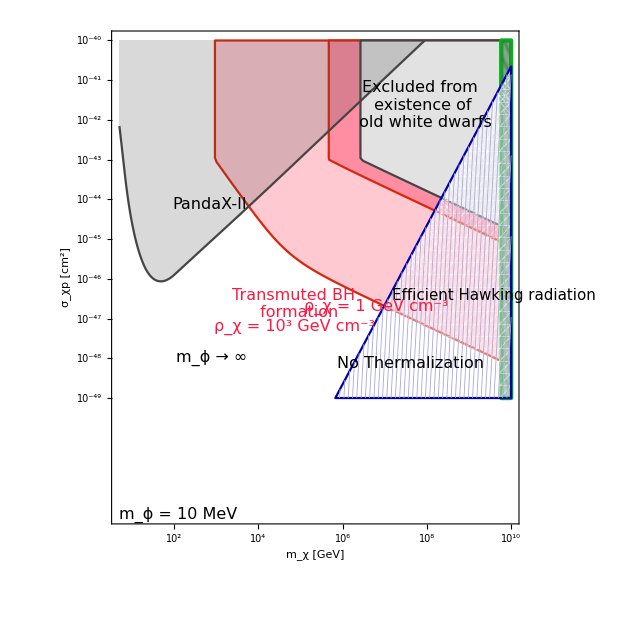

```mathematica
pv3=Show[Plot[-42,{x,1,8},PlotRange->{{2,10},{-44,-53}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χp [cm^2]",FontSize->20]},ImageSize->620,FrameTicks->myticks,AspectRatio->1],
RegionPlot[{10^3/0.4*totcapuni[10^x,10^y]≥Max[ Nself[10^x,10^7],NchBoson[10^x]]},{x,2,10},{y,-44,-53},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],PlotStyle->RGBColor["#FFC9D2"],BoundaryStyle->RGBColor["#DB260B"],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,ImageSize->600,FrameTicks->myticks],

RegionPlot[{1/0.4*totcapuni[10^x,10^y]≥Max[ Nself[10^x,10^7],NchBoson[10^x]]},{x,2,10},{y,-44,-53},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],PlotStyle->RGBColor["#FF8EA2"],BoundaryStyle->RGBColor["#DB260B"],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,ImageSize->600,FrameTicks->myticks],


RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,10^7],NchBoson[10^x]]},{x,2,10},{y,-44,-53},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},BoundaryStyle->Directive[RGBColor["#454545"]],PlotStyle->Directive[RGBColor["#E2E2E2"]],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],

ListPlot[{Table[{data10[[i,1]],data10[[i,2]]-4},{i,Length[data10]}]},PlotRange->{{2,10},{-44,-53}},PlotStyle->Directive[RGBColor["#454545"]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->600,AspectRatio->1,Joined->True,Filling->Top,FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,InterpolationOrder->2,FrameTicks->myticks],


RegionPlot[{10^x≥ 5.8*10^9},{x,2,10},{y,-44,-53},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],MeshFunctions->{20*#1-#2&},Mesh->25,MeshStyle->Directive[RGBColor["#3A7D44"],Thickness[0.001]],PlotStyle->Directive[White,Opacity[0.4]],BoundaryStyle->Directive[RGBColor["#02B51D"],Thickness[0.005]],PlotRangePadding->None,ImageSize->500],

RegionPlot[{ttherm[10^x,10^y,10^7]≥  tage},{x,2,10},{y,-44,-53},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],BoundaryStyle->Darker[Blue],PlotStyle->Directive[White,Opacity[0.4]],MeshFunctions->{20*#1-#2&},Mesh->40,MeshStyle->Directive[RGBColor["#AAA6DF"],Thickness[0.001]],FrameLabel->{Style["Log_10 [m_x] [GeV]",FontSize->20,Bold],Style["Log_10 [σ_xn] [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500],Graphics[Rotate[Text[Style["Efficient Hawking radiation",Darker[Black],FontSize->15],{9.6,-50.43}],90 Degree]],Graphics[Rotate[Text[Style["Excluded from \n existence of \n old white dwarfs",Darker[Black],FontSize->16],{7.9,-45.63}],0 Degree]],Graphics[Rotate[Text[Style["No Thermalization",Darker[Black],FontSize->16],{7.6,-52.13}],0 Degree]],Graphics[Rotate[Text[Style["PandaX-II",Darker[Black],FontSize->16],{2.85,-48.13}],0 Degree]],Graphics[Rotate[Text[Style[Framed["m_ϕ = 10 MeV"],Darker[Black],FontSize->16],{2.1,-55.93}],0 Degree]],Graphics[Rotate[Text[Style["Transmuted BH \n formation",RGBColor["#FF1841"],FontSize->16],{4.9,-50.63}],0 Degree]],Graphics[Text[Style["ρ_χ = 10^3 GeV cm^-3",RGBColor["#FF1841"],FontSize->16],Scaled[{0.45,0.4}],Scaled[{0.16,1.05}],{1.,-0.45}]],Graphics[Text[Style["ρ_χ = 1 GeV cm^-3",RGBColor["#FF1841"],FontSize->16],Scaled[{0.65,0.44}],Scaled[{0.85,-1.65}],{0.4,-0.2}]],Graphics[Rotate[Text[Style[Framed["m_ϕ → ∞"],Darker[Black],FontSize->16],{2.9,-51.99}],0 Degree]]]//Quiet
```

```mathematica
Export["TBH_WD_Boson.pdf",pv3];
```

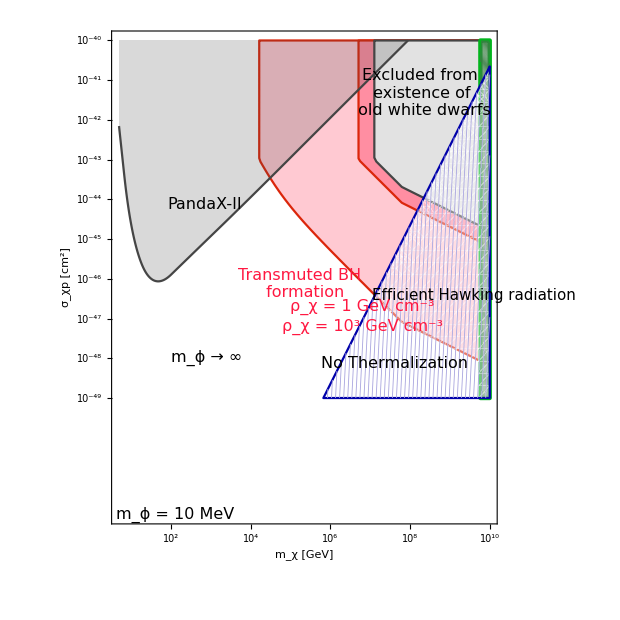

```mathematica
pv4=Show[Plot[-42,{x,1,8},PlotRange->{{2,10},{-44,-53}},PlotStyle->Directive[{Dashing[Medium],Black},Thickness[0.004]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χp [cm^2]",FontSize->20]},ImageSize->620,FrameTicks->myticks,AspectRatio->1],
RegionPlot[{10^3/0.4*totcapuni[10^x,10^y]≥Max[ Nself[10^x,10^7],NchFermion[10^x]]},{x,2,10},{y,-44,-53},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],PlotStyle->RGBColor["#FFC9D2"],BoundaryStyle->RGBColor["#DB260B"],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,ImageSize->600,FrameTicks->myticks],

RegionPlot[{1/0.4*totcapuni[10^x,10^y]≥Max[ Nself[10^x,10^7],NchFermion[10^x]]},{x,2,10},{y,-44,-53},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],PlotStyle->RGBColor["#FF8EA2"],BoundaryStyle->RGBColor["#DB260B"],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,ImageSize->600,FrameTicks->myticks],


RegionPlot[{totcapuni[10^x,10^y]≥Max[ Nself[10^x,10^7],NchFermion[10^x]]},{x,2,10},{y,-44,-53},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.0035]],FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},BoundaryStyle->Directive[RGBColor["#454545"]],PlotStyle->Directive[RGBColor["#E2E2E2"]],PlotRangePadding->None,ImageSize->500,FrameTicks->myticks],

ListPlot[{Table[{data10[[i,1]],data10[[i,2]]-4},{i,Length[data10]}]},PlotRange->{{2,10},{-44,-53}},PlotStyle->Directive[RGBColor["#454545"]],Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],ImageSize->600,AspectRatio->1,Joined->True,Filling->Top,FrameLabel->{Style["m_χ [GeV]",FontSize->20],Style["σ_χn [cm^2]",FontSize->20]},PlotRangePadding->None,InterpolationOrder->2,FrameTicks->myticks],


RegionPlot[{10^x≥ 5.8*10^9},{x,2,10},{y,-44,-53},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],MeshFunctions->{20*#1-#2&},Mesh->25,MeshStyle->Directive[RGBColor["#3A7D44"],Thickness[0.001]],PlotStyle->Directive[White,Opacity[0.4]],BoundaryStyle->Directive[RGBColor["#02B51D"],Thickness[0.005]],PlotRangePadding->None,ImageSize->500],

RegionPlot[{ttherm[10^x,10^y,10^7]≥  tage},{x,2,10},{y,-44,-53},PlotPoints->30,Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],BoundaryStyle->Darker[Blue],PlotStyle->Directive[White,Opacity[0.4]],MeshFunctions->{20*#1-#2&},Mesh->40,MeshStyle->Directive[RGBColor["#AAA6DF"],Thickness[0.001]],FrameLabel->{Style["Log_10 [m_x] [GeV]",FontSize->20,Bold],Style["Log_10 [σ_xn] [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500],Graphics[Rotate[Text[Style["Efficient Hawking radiation",Darker[Black],FontSize->15],{9.6,-50.43}],90 Degree]],Graphics[Rotate[Text[Style["Excluded from \n existence of \n old white dwarfs",Darker[Black],FontSize->16],{8.3,-45.33}],0 Degree]],Graphics[Rotate[Text[Style["No Thermalization",Darker[Black],FontSize->16],{7.6,-52.13}],0 Degree]],Graphics[Rotate[Text[Style["PandaX-II",Darker[Black],FontSize->16],{2.85,-48.13}],0 Degree]],Graphics[Rotate[Text[Style[Framed["m_ϕ = 10 MeV"],Darker[Black],FontSize->16],{2.1,-55.93}],0 Degree]],Graphics[Rotate[Text[Style["Transmuted BH \n formation",RGBColor["#FF1841"],FontSize->16],{5.3,-50.13}],0 Degree]],Graphics[Text[Style["ρ_χ = 10^3 GeV cm^-3",RGBColor["#FF1841"],FontSize->16],Scaled[{0.65,0.4}],Scaled[{0.85,1.55}],{0.7,-0.6}]],Graphics[Text[Style["ρ_χ = 1 GeV cm^-3",RGBColor["#FF1841"],FontSize->16],Scaled[{0.65,0.44}],Scaled[{0.85,-1.65}],{0.4,-0.35}]],Graphics[Rotate[Text[Style[Framed["m_ϕ → ∞"],Darker[Black],FontSize->16],{2.9,-51.99}],0 Degree]]]//Quiet
```

```mathematica
Export["TBH_WD_Fermion.pdf",pv4];
```